Implementing counter machines
by Sam Natarajan

The objective of this project was to implement counter machines in the Wolfram Language and establish which counter machine was the most unpredictable. I designed a general counter machine function and used this function to demonstrate 5 types of counter machines. Finally, I determined which counter machines were unpredictable and explored complexity by adding more registers.

## An Introduction to Counter Machines

Counter machines operate on a list of numbers based off a set of instructions. They have multiple registers, or slots, each of which holds a single non-negative integer. In this project, the main focus is counter machines with two registers, but three-register counter machines are analyzed as well.  Each type of counter machine has a defined set of instructions, and the counter machine executes these instructions on the registers. There are many different types of counter machines, characterized by their instruction sets.

Each instruction for a counter machine references an operator, such as increment (inc), decrement (dec), and jump (j).

Show an example of a counter machine instruction set:

```mathematica
{inc[r1], dec[r2], j[1]};
```

These operators change the values of each register and/or the current instruction. There are approximately 10 operators: 5 are standard operators and the rest are conditional operators. Most counter machine instructions reference a couple standard operators and one conditional operator.

## Creating a Counter Machine Function

### Creating and Running a Counter Machine

A counter machine is expressed in the form {z, {r1, r2, r3 ...}}. The first item, z, represents the current instruction the counter machine is evaluating, and {r1, r2, r3...} are the registers. Using this information, one can create a generic counter machine using Table, shown in the code below.

Create an empty counter machine with Table:

```mathematica
counterMachine[n_Integer]:= {1, Table[0, n]};
```

In Stephen Wolfram's book, A New Kind of Science, he writes the following two functions to run a generic counter machine.

Evolve a counter machine by nesting steps from an instruction set:

```mathematica
cmEvolveList[program_, init: {_Integer, _List}, t_Integer]:= NestList[cmStep[program, #]&, init, t]
cmStep[program_, {n_Integer, list_List}]:= If[n > Length[program], {1, list}, cmExecute[program[[n]], {n, list}]]
```

Given a list of instructions, an initial counter machine, and the number of times to run the counter machine, the first function above utilizes a NestList to run the counter machine. The second function runs each individual iteration of the counter machine. If the current instruction is beyond the amount of instructions provided, the current instruction z resets to 1; otherwise, the function executes the current instruction.

### Counter Machine Operators

Each instruction references a counter machine operator. There are many operators for counter machines; each is explained below with its code.

Increment (INC) - Increase the value of register r by 1:

```mathematica
cmExecute[inc[r_,z_], {n_, list_}]:= {z, MapAt[(#+1)&, list, r]}
cmExecute[inc[r_], {n_, list_}]:= cmExecute[inc[r,(n+1)],{n,list}]
```

The first increment function has the next instruction explicitly specified.

The second increment function simply goes to the next instruction.

Decrement (DEC) - Decrease the value of register r by 1:

```mathematica
cmExecute[dec[r_, z_], {n_, list_}]:= If[list[[r]] ≤ 0,{n+1,list},{z, MapAt[(#-1)&, list, r]}]
cmExecute[dec[r_], {n_, list_}]:= cmExecute[dec[r,(n+1)],{n,list}]
```

The first decrement function has the next instruction explicitly specified.

The second decrement function simply goes to the next instruction.

Clear (CLR) - Set register r to 0:

```mathematica
cmExecute[clr[r_], {n_, list_}]:= {n+1, MapAt[0 &, list, r]}
```

Copy (CPY) - Copy the value of register r1 to register r2:

```mathematica
cmExecute[cpy[r1_, r2_], {n_, list_}]:= {n+1, MapAt[list[[r1]]&, list, r2]}
```

Jump (J) - Jump to instruction z:

```mathematica
cmExecute[j[z_], {n_, list_}]:= {z, list}
```

Jump if Zero (JZ) - If the value in register r is 0, then jump to instruction z; otherwise continue to the next instruction:

```mathematica
cmExecute[jz[r_, zTrue_, zFalse_], {n_, list_}]:= If[list[[r]] == 0, {zTrue, list}, {zFalse, list}]
```

Jump if Not Zero (JNZ) - If the value in register r is not 0, then jump to instruction z; otherwise continue to the next instruction:

```mathematica
cmExecute[jnz[r_, zTrue_, zFalse_], {n_,list_}]:= If[list[[r]] ≠ 0,{zTrue,list},{zFalse,list}]
```

Jump if Zero or Decrement (JZDEC) - If the value in register r is 0, then jump to instruction z; otherwise decrement the value in register r:

```mathematica
cmExecute[jzdec[r_, zTrue_, zFalse_], {n_, list_}]:= If[list[[r]] == 0, {zTrue, list}, cmExecute[dec[r, zFalse], {n, list}]]
```

Jump if Equal (JE) - If the value in register r1 is equal to the value in register r2, then jump to instruction z; otherwise continue to the next instruction:

```mathematica
cmExecute[je[r1_, r2_, zTrue_,zFalse_],{n_,list_}]:=If[list[[r1]]==list[[r2]], {zTrue,list}, {zFalse,list}]
```

### Final Counter Machine Function

Putting all these functions together creates a generic counter machine function.

Create the final counter machine function:

```mathematica
counterMachine[n_Integer]:= {1, Table[0, n]};

cmEvolveList[program_, init:{_Integer, _List}, t_Integer]:= NestList[cmStep[program, #]&,init,t]
cmStep[program_, {n_Integer, list_List}]:= If[n > Length[program],{1,list},cmExecute[program[[n]],{n, list}]]

cmExecute[inc[r_,z_], {n_, list_}]:= {z, MapAt[(#+1)&,list,r]}
cmExecute[inc[r_], {n_, list_}]:= cmExecute[inc[r,(n+1)],{n,list}]
cmExecute[dec[r_, z_], {n_, list_}]:= If[list[[r]] ≤ 0,{n+1,list},{z, MapAt[(#-1)&, list, r]}]
cmExecute[dec[r_], {n_, list_}]:= cmExecute[dec[r,(n+1)],{n,list}]
cmExecute[clr[r_],{n_,list_}]:= {n+1, MapAt[0 &,list,r]}
cmExecute[cpy[r1_, r2_],{n_,list_}]:= {n+1, MapAt[list[[r1]]&,list,r2]}
cmExecute[j[z_],{n_,list_}]:= {z, list}
cmExecute[jz[r_, zTrue_, zFalse_], {n_, list_}]:= If[list[[r]] == 0, {zTrue, list}, {zFalse, list}]
cmExecute[jnz[r_,zTrue_,zFalse_],{n_,list_}]:= If[list[[r]] ≠ 0,{zTrue,list},{zFalse,list}]
cmExecute[jzdec[r_,zTrue_,zFalse_],{n_,list_}]:= If[list[[r]] == 0,{zTrue,list},cmExecute[dec[r,zFalse],{n,list}]]
cmExecute[je[r1_, r2_, zTrue_,zFalse_],{n_,list_}]:= If[list[[r1]] == list[[r2]], {zTrue,list}, {zFalse,list}]
```

The function above, when tested on a random counter machine, works perfectly.

Run a two-register counter machine with 5 instructions for 10 steps:

```mathematica
cm = counterMachine[2];
instructions={inc[1],dec[2,1],inc[2],dec[1,3],dec[2,1]};
cmEvolveList[instructions,cm, 10]
```

{{1,{0,0}},{2,{1,0}},{3,{1,0}},{4,{1,1}},{3,{0,1}},{4,{0,2}},{5,{0,2}},{1,{0,1}},{2,{1,1}},{1,{1,0}},{2,{2,0}}}

## Types of Counter Machines

### Counter Machine Instruction Sets

There are 5 main types of counter machines, characterized by their instruction sets. Essentially, each type of counter machine has a specific set of instructions in a specific order. These 5 types are the Shepherdson-Sturgis machine, the Minsky machine (aka the Abacus machine/Lambek machine), the Program machine/Program computer, the Successor machine, and the Elgot-Robinson model. Each counter machine's instruction is shown below.

Note: The variables used in the machine instruction set are arbitrary; the instructions in the set and the order of the instructions is what matters.

Show the instruction set for a Shepherdson-Sturgis machine:

```mathematica
{INC[r], DEC[r], CLR[r], CPY[r1, r2], JNZ[r, z], J[z]};
```

Show the instruction set for a Minsky machine (aka Abacus machine/Lambek machine):

```mathematica
{INC[r, z], JZDEC[r, zTrue, zFalse]};
```

Show the instruction set for a Program machine/Program computer:

```mathematica
{INC[r], DEC[r], JZ[r, rTrue]};
```

Show the instruction set for a Successor machine:

```mathematica
{CLR[r], INC[r], JE[r1, r2, z]};
```

Show the instruction set for an Elgot-Robinson model:

```mathematica
{INC[r], CPY[r1, r2], JE[r1, r1, z]};
```

### Modeling Counter Machines

Using the counter machine and the instruction set created above, the different counter machines can be evaluated for any number of steps. The counter machine is expressed with Grid and ArrayPlot, displayed side-by-side with GraphicsRow. For the grid, the left side shows the current instruction and the right side shows the registers. For the ArrayPlot, the leftmost column is the instruction, the middle column shows the value of register 1, and the right column shows the value of register 2. 

Note: For the ArrayPlot, the colors get darker as the number increases. If two colors are the same, they have the same value.

#### Shepherdson-Sturgis Machine

Model the evolution of a Shepherdson-Sturgis machine for 15 steps:

```mathematica
Module[{ssMachine = counterMachine[2],ssMachineInstructions={inc[1],dec[2],clr[1],cpy[2,1],jnz[2,3,6],j[1]},ssMachineTable},
ssMachineTable=cmEvolveList[ssMachineInstructions,ssMachine,15];
GraphicsRow[{Style[Grid[ssMachineTable, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[ssMachineTable],3],Mesh->True]}]]
```

-Graphics-

#### Minsky Machine (aka Abacus Machine/Lambek Machine)

Model the evolution of a Minsky machine for 15 steps:

```mathematica
Module[{minskyMachine=counterMachine[2],minskyMachineInstructions={inc[1,2],jzdec[2,1,2]},minskyMachineTable},
minskyMachineTable=cmEvolveList[minskyMachineInstructions,minskyMachine,15];
GraphicsRow[{Style[Grid[minskyMachineTable, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[minskyMachineTable],3],Mesh->True]}]]
```

-Graphics-

#### Program Machine/Program Computer

Model the evolution of a Program machine for 15 steps:

```mathematica
Module[{pMachine=counterMachine[2],pMachineInstructions={inc[2],dec[1],jz[2,2,1]},pMachineTable},
pMachineTable=cmEvolveList[pMachineInstructions,pMachine,15];
GraphicsRow[{Style[Grid[pMachineTable, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[pMachineTable],3],Mesh->True]}]]
```

-Graphics-

#### Successor Machine

Model the evolution of a Successor machine for 15 steps:

```mathematica
Module[{succMachine=counterMachine[2],succMachineInstructions={clr[2],inc[2],je[2,1,2,1]},succMachineTable},
succMachineTable=cmEvolveList[succMachineInstructions,succMachine,15];
GraphicsRow[{Style[Grid[succMachineTable, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[succMachineTable],3],Mesh->True]}]]
```

-Graphics-

#### Elgot-Robinson Model

Model the evolution of an Elgot-Robinson model for 15 steps:

```mathematica
Module[{erMachine=counterMachine[2],erMachineInstructions={inc[1],cpy[1,2],je[1,2,1,1]},erMachineTable},
erMachineTable=cmEvolveList[erMachineInstructions,erMachine,15];
GraphicsRow[{Style[Grid[erMachineTable, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[erMachineTable],3],Mesh->True]}]]
```

-Graphics-

## Establishing Unpredictability

### Predictability Functions

Armed with a counter machine function, the final goal of this project is to find which counter machine, of the types stated above, is the most unpredictable. To find the most unpredictable counter machine, the first step is to create functions that determine predictability.

One necessary function is one that checks for repeating register values over many iterations of the counter machine. The built-in function FindTransientRepeat finds repeats with a transient in a list (a transient is a beginning "phrase" of values that aren't included in the repeats). To create a function that finds repeating register values, the function FindTransientRepeat is applied to a list of register values; if FIndTransientRepeat returns an empty list, there is no repeat.

Check for repeating register values:

```mathematica
checkRepeat[cm_List]:= Length[FindTransientRepeat[cm[[All, 2]], 4][[2]]]==0
```

Another necessary function is one that searches for a pattern in the register values. The function FindSequenceFunction is the best option in this situation. FindSequenceFunction finds a function that can express a list of values. If the register values appear in a pattern, the FindSequenceFunction will most likely find it.

To create a function that checks for a pattern in the register values, FindSequenceFunction is applied to the register values from the counter machine function. If FindSequenceFunction can’t find a way to express the input list, it’ll return an expression with the head FindSequenceFunction, which means the counter machine doesn’t have a pattern.

Search for a pattern in register values:

```mathematica
checkPattern[cm_List]:= Head[FindSequenceFunction[Flatten[cm[[All, 2]]], TimeConstraint -> 3]] === FindSequenceFunction
```

Using these two functions, a general predictability function can be written. Essentially, when given counter machine values, it checks if checkrepeat and checkpattern can find repeating values or a pattern; if neither function can, then the counter machine input is unpredictable.

Use checkRepeat and checkPattern to create a predictability function:

```mathematica
predictabilityTest[cm_List]:= If[checkRepeat[cm] && checkPattern[cm], "Unpredictable", "Predictable"]
```

Below, the predictabilityTest function is tested with the 5 examples of counter machine instructions used above. In these tests, the counter machine function executes for 30 steps.

Shepherdson-Sturgis Machine

Run predictabilityTest on a random Shepherdson-Sturgis machine:

```mathematica
ssPredictabilityTest=cmEvolveList[{inc[1],dec[2],clr[1],cpy[2,1],jnz[2,3,6],j[1]},counterMachine[2],30];
predictabilityTest[ssPredictabilityTest]
```

Predictable

Minsky Machine (aka Abacus Machine/Lambek Machine)

Run predictabilityTest on a random Minsky machine:

```mathematica
minskyPredictabilityTest=cmEvolveList[{inc[1,2],jzdec[2,1,2]},counterMachine[2],30];
predictabilityTest[minskyPredictabilityTest]
```

Predictable

Program Machine/Program Computer

Run predictabilityTest on a random Program machine:

```mathematica
programPredictabilityTest=cmEvolveList[{inc[2],dec[1],jz[2,2,1]},counterMachine[2],30];
predictabilityTest[programPredictabilityTest]
```

Predictable

Successor Machine

Run predictabilityTest on a random Successor machine:

```mathematica
succPredictabilityTest=cmEvolveList[{clr[2],inc[2],je[2,1,2,1]},counterMachine[2],30];
predictabilityTest[succPredictabilityTest]
```

Predictable

Elgot-Robinson Model

Run predictabilityTest on a random Elgot-Robinson model:

```mathematica
erPredictabilityTest=cmEvolveList[{inc[1],cpy[1,2],je[1,2,1,1]},counterMachine[2],30];
predictabilityTest[erPredictabilityTest]
```

Predictable

As expected, the function determined that all 5 counter machine examples tested were predictable.

### Unpredictable Counter Machines

The predictabilityTest function can now be used on the 5 types of counter machines in order to find ones that are not predictable. For each type of counter machine, the predictabilityTest function will be applied to every possible permutation of values for the corresponding instruction set. Using the function Table to iterate over the possible values for each variable creates a list of possible permutations. After finding counter machines that aren't predictable, they can be analyzed to determine whether or not they're truly unpredictable.

Note: The computations run below can take some time to run, due to the volume of possibilities.

Shepherdson-Sturgis Machine: 13824 possibilities

Minsky Machine: 32 possibilities

Program Machine: 72 possibilities

Successor Machine: 144 possibilities

Elgot-Robinson Model: 288 possibilities

Find the Shepherdson-Sturgis machine instruction sets that create unpredictable counter machines:

```mathematica
alPossibleSSMachines= Flatten[Table[{inc[r1],dec[r2],clr[r3],cpy[r4,r5],jnz[r6,z1,z2],j[z3]},{r1,2},{r2,2},{r3,2},{r4,2},{r5,2},{r6, 2},{z1, 6},{z2, 6},{z3,6}],8];
predictabilitySS=If[predictabilityTest[cmEvolveList[#,counterMachine[2],30]]=="Unpredictable",#,Nothing]&/@alPossibleSSMachines
```

{{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,1],j[6]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,4],j[3]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,5],j[1]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,5],j[2]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,5],j[3]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,6],j[1]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,6],j[2]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,6],j[5]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,1,6],j[6]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,6,1],j[1]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,6,2],j[1]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,6,3],j[1]},{inc[1],dec[2],clr[2],cpy[1,2],jnz[1,6,4],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,1,3],j[4]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,1,3],j[6]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,1,6],j[6]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,1],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,2],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,3],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,4],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,5],j[1]},{inc[2],dec[1],clr[1],cpy[2,1],jnz[2,6,6],j[1]}}

Find the Minsky machine instruction sets that create unpredictable counter machines:

```mathematica
allPossibleMinskyMachines= Flatten[Table[{inc[r1,z1],jzdec[r2,z2,z3]},{r1,2},{r2,2},{z1,2},{z2,2},{z3,2}],4];
predictabilityMinsky=If[predictabilityTest[cmEvolveList[#,counterMachine[2],30]]=="Unpredictable",#,Nothing]&/@allPossibleMinskyMachines
```

{}

Find the Program machine instruction sets that create unpredictable counter machines:

```mathematica
allpossiblePMachines= Flatten[Table[{inc[r1],dec[r2],jz[r3,z1,z2]}, {r1,2},{r2,2},{r3,2},{z1,3},{z2,3}],4];
predictabilityProgram=If[predictabilityTest[cmEvolveList[#,counterMachine[2],30]]=="Unpredictable",#,Nothing]&/@allpossiblePMachines
```

{}

Find the Successor machine instruction sets that create unpredictable counter machines:

```mathematica
allPossibleSuccMachines=Flatten[Table[{clr[r1],inc[r2],je[r3,r4,z1,z2]},{r1,2},{r2,2},{r3,2},{r4,2},{z1,3},{z2,3}],5];
predictabilitySUCC=If[predictabilityTest[cmEvolveList[# ,counterMachine[2],30]]=="Unpredictable",#,Nothing]&/@allPossibleSuccMachines
```

{}

Find the Elgot-Robinson model instruction sets that create unpredictable counter machines:

```mathematica
allPossibleErMachines= Flatten[Table[{inc[r1],cpy[r2,r3],je[r4,r5,z1,z2]},{r1,2},{r2,2},{r3,2},{r4,2},{r5, 2},{z1,3},{z2,3}],6];
predictabilityER=If[predictabilityTest[cmEvolveList[#,counterMachine[2],30]]=="Unpredictable",#,Nothing]&/@allPossibleErMachines
```

{}

Tests for the Minsky machine, the Program machine, the Successor machine, and the Elgot-Robinson model didn't return any instruction sets marked unpredictable. However, the Shepherdson-Sturgis machine tests returned 22 possible unpredictable instruction sets. With this list, the first step is to eliminate any instruction sets that return duplicate counter machines.

Delete duplicate counter machines from the list of instruction sets:

```mathematica
predictabilitySS=;
ssPossibilities=DeleteDuplicates[cmEvolveList[#,counterMachine[2],15]&/@predictabilitySS]
```

{{{1,{0,0}},{2,{1,0}},{3,{1,0}},{4,{1,0}},{5,{1,1}},{1,{1,1}},{2,{2,1}},{3,{2,0}},{4,{2,0}},{5,{2,2}},{1,{2,2}},{2,{3,2}},{3,{3,1}},{4,{3,0}},{5,{3,3}},{1,{3,3}}},{{1,{0,0}},{2,{1,0}},{3,{1,0}},{4,{1,0}},{5,{1,1}},{6,{1,1}},{1,{1,1}},{2,{2,1}},{3,{2,0}},{4,{2,0}},{5,{2,2}},{6,{2,2}},{1,{2,2}},{2,{3,2}},{3,{3,1}},{4,{3,0}}},{{1,{0,0}},{2,{0,1}},{3,{0,1}},{4,{0,1}},{5,{1,1}},{1,{1,1}},{2,{1,2}},{3,{0,2}},{4,{0,2}},{5,{2,2}},{1,{2,2}},{2,{2,3}},{3,{1,3}},{4,{0,3}},{5,{3,3}},{1,{3,3}}},{{1,{0,0}},{2,{0,1}},{3,{0,1}},{4,{0,1}},{5,{1,1}},{6,{1,1}},{1,{1,1}},{2,{1,2}},{3,{0,2}},{4,{0,2}},{5,{2,2}},{6,{2,2}},{1,{2,2}},{2,{2,3}},{3,{1,3}},{4,{0,3}}}}

Visualizing these counter machines would make it easier to understand whether or not these counter machines are truly unpredictable.

Use Grid and ArrayPlot to model the counter machines:

```mathematica
GraphicsRow[{Style[Grid[#, Frame->All],RGBColor[0.8,0.36,0.41],17],ArrayPlot[Partition[Flatten[#],3],Mesh->True]}]&/@ssPossibilities
```

-Graphics-

Looking at the models shown above, it's quite evident that these counter machines have a pattern; however, this pattern wasn't picked up by the checkPattern function. This means that ultimately, none of the 5 types of two-register counter machines produce a completely unpredictable counter machine.

## Complexity with More Registers

### Analyzing Three-Register Counter Machines

All possible two-register counter machines of the 5 types are predictable. However, a more complex counter machine could possibly be unpredictable. That means the logical next question is if adding more registers creates more complexity.

The first step is to analyze and compare the differences between 2 and 3 registers. The Minsky machine is best for this comparison, since it has the smallest number of possibilities to explore.

Create a two-register and three-register Minsky machine:

```mathematica
minskyTwoReg = cmEvolveList[#,counterMachine[2],30] &/@ Flatten[Table[{inc[r1,z1],jzdec[r2,z2,z3]},{r1,2},{r2,2},{z1,2},{z2,2},{z3,2}],4];
minskyThreeReg = cmEvolveList[#,counterMachine[3],30] &/@ Flatten[Table[{inc[r1,z1],jzdec[r2,z2,z3]},{r1,3},{r2,3},{z1,2},{z2,2},{z3,2}],4];
```

With this, the next step is to model a few Minsky machines to look for any similarities or differences.

Model the first 10 two-register and three-register Minsky machines:

```mathematica
mTwo=minskyTwoReg[[1;;10]];
mThree=minskyThreeReg[[1;;10]];
GraphicsRow[{ArrayPlot[Partition[Flatten[#],3],Mesh->True]}]&/@mTwo
GraphicsRow[{ArrayPlot[Partition[Flatten[#],4],Mesh->True]}]&/@mThree
```

-Graphics-

-Graphics-

Comparing the models, it becomes clear that the register values for two and three register Minsky machines are close to identical. The only differences are caused by the three-register Minsky machine having one more empty register. Hence, a reasonable hypothesis is that the register values for all two-register Minsky machines are identical to the register values for all three-register Minsky machines.

To prove this, the steps are: 1) finding the register values for all two-register and three-register Minsky machines, 2) eliminating 0's (as they represent empty registers), 3) deleting duplicates, and 4) checking if the resultant lists of two-register and three-register values are the same.

Follow the steps above for two-register and three-register Minsky machines:

```mathematica
minskyTwoValues=DeleteDuplicates[Table[Flatten[minskyTwoReg[[n,All,2]]]/. 0->Nothing,{n,Length[minskyTwoReg]}]];
minskyThreeValues=DeleteDuplicates[Table[Flatten[minskyThreeReg[[n,All,2]]]/. 0->Nothing,{n,Length[minskyThreeReg]}]];
minskyTwoValues==minskyThreeValues
```

True

Clearly, the values for two-register and three-register Minsky machines are identical. When the same steps are used to test the other 4 types of counter machines, the results are clear.

Check if two-register and three-register Shepherdson-Sturgis machines are identical:

```mathematica
ssTwoReg = cmEvolveList[#,counterMachine[2],30] &/@ Flatten[Table[{inc[r1],dec[r2],clr[r3],cpy[r4,r5],jnz[r6,z1,z2],j[z]},{r1,2},{r2,2},{r3,2},{r4,2},{r5,2},{r6, 2},{z1, 6},{z2, 6},{z,6}],8];
ssThreeReg = cmEvolveList[#,counterMachine[3],30] &/@ Flatten[Table[{inc[r1],dec[r2],clr[r3],cpy[r4,r5],jnz[r6,z1,z2],j[z]},{r1,3},{r2,3},{r3,3},{r4,3},{r5,3},{r6, 3},{z1, 6},{z2, 6},{z,6}],8];
ssTwoValues=DeleteDuplicates[Table[Flatten[ssTwoReg[[n,All,2]]]/. 0->Nothing,{n,Length[ssTwoReg]}]];
ssThreeValues=DeleteDuplicates[Table[Flatten[ssThreeReg[[n,All,2]]]/. 0->Nothing,{n,Length[ssThreeReg]}]];
ssTwoValues==ssThreeValues
```

False

Check if two-register and three-register Program machines are identical:

```mathematica
programTwoReg=cmEvolveList[#,counterMachine[2],30] &/@ Flatten[Table[{inc[r1],dec[r2],jz[r3,z1,z2]}, {r1,2},{r2,2},{r3,2},{z1,3},{z2,3}],4];
programThreeReg = cmEvolveList[#,counterMachine[3],30] &/@ Flatten[Table[{inc[r1],dec[r2],jz[r3,z1,z2]}, {r1,3},{r2,3},{r3,3},{z1,3},{z2,3}],4];
programTwoValues=DeleteDuplicates[Table[Flatten[programTwoReg[[n,All,2]]]/. 0->Nothing,{n,Length[programTwoReg]}]];
programThreeValues = DeleteDuplicates[Table[Flatten[programThreeReg[[n,All,2]]]/. 0->Nothing,{n,Length[programThreeReg]}]];
programTwoValues== programThreeValues
```

True

Check if two-register and three-register Successor machines are identical:

```mathematica
succTwoReg=cmEvolveList[#,counterMachine[2],30] &/@ Flatten[Table[{clr[r1],inc[r2],je[r3,r4,z1,z2]},{r1,2},{r2,2},{r3,2},{r4,2},{z1,3},{z2,3}],5];
succThreeReg = cmEvolveList[#,counterMachine[3],30] &/@ Flatten[Table[{clr[r1],inc[r2],je[r3,r4,z1,z2]},{r1,3},{r2,3},{r3,3},{r4,3},{z1,3},{z2,3}],5];
succTwoValues=DeleteDuplicates[Table[Flatten[succTwoReg[[n,All,2]]]/. 0->Nothing,{n,Length[succTwoReg]}]];
succThreeValues = DeleteDuplicates[Table[Flatten[succThreeReg[[n,All,2]]]/. 0->Nothing,{n,Length[succThreeReg]}]];
succTwoValues== succThreeValues
```

True

Check if two-register and three-register Elgot-Robinson models are identical:

```mathematica
erTwoReg=cmEvolveList[#,counterMachine[2],30] &/@ 
Flatten[Table[{inc[r1],cpy[r2,r3],je[r4,r5,z1,z2]},{r1,2},{r2,2},{r3,2},{r4,2},{r5, 2},{z1,3},{z2,3}],6];
erThreeReg = cmEvolveList[#,counterMachine[3],30] &/@ Flatten[Table[{inc[r1],cpy[r2,r3],je[r4,r5,z1,z2]},{r1,3},{r2,3},{r3,3},{r4,3},{r5, 3},{z1,3},{z2,3}],6];
erTwoValues=DeleteDuplicates[Table[Flatten[erTwoReg[[n,All,2]]]/. 0->Nothing,{n,Length[erTwoReg]}]];
erThreeValues = DeleteDuplicates[Table[Flatten[erThreeReg[[n,All,2]]]/. 0->Nothing,{n,Length[erThreeReg]}]];
erTwoValues== erThreeValues
```

True

Only the Shepherdson-Sturgis counter machine shows a difference between values in two and three registers. Now, the next step is to check whether or not these differences could cause unpredictability. Demonstrating the values with an ArrayPlot reveals a pattern, that while complex, renders these counter machines predictable.

Visualize the unique three-register values for a Shepherdson-Sturgis machine:

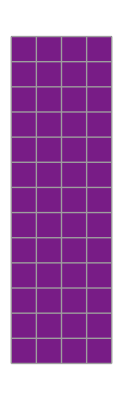
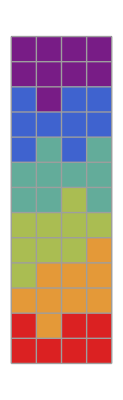
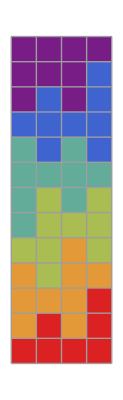
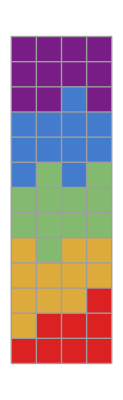
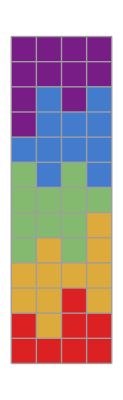
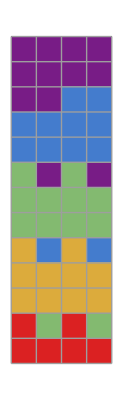
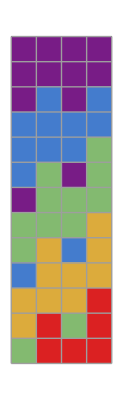
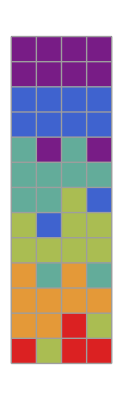

```mathematica
ssDiff=Complement[ssThreeValues,ssTwoValues];
ArrayPlot[Partition[Flatten[#],4],Mesh->True, ColorFunction->"Rainbow"]&/@ssDiff
```

It is evident that most two-register and three-register counter machines (of the 5 types) have identical values, and of the few counter machines that only occur with three registers, none of them are predictable. Therefore, while three-register counter machines create slightly more complex patterns than two-register counter machine, they do not cause unpredictability. Whether or not this holds up for counter machines with more registers is another question entirely.

## Conclusion

The general counter machine function works well and can be used to quickly generate register values for any counter machine provided an instruction set and the number of steps. Using Grid and ArrayPlot together in a GraphicsRow produces a helpful model of counter machines register values over many steps. The predictabilityTest function written for this project is mostly capable of determining a counter machine's predictability. Using these functions and methods to analyze the 5 types of counter machines demonstrated that while some counter machines had relatively complex patterns, none of them were completely unpredictable. After adding another register to explore complexity, it became clear that very few counter machines with different values were created and all were predictable.

#### Future Plans

In the future, I plan to improve my predictabilityTest function, so that it's capable of perfectly determining whether or not a counter machine is predictable. I also want to explore the predictability of counter machines as more and more registers are added. Finally, I hope to use my improved predictabilityTest function to analyze many more counter machines (with more instructions, perhaps) in order to find a counter machine that is completely unpredictable. There's a lot left to explore when it comes to counter machines, and I've barely scratched the surface.